```mathematica
$LoadFeynArts= True;
<<FeynCalc`
```

FeynCalc is already loaded! To reload it, please restart the kernel.

$Aborted

```mathematica
$D[i_]:=$dall/.TopologyList[mask__][ds__]:>TopologyList[mask][Sequence@@List[ds][[i]]];
```

Excluding 0 Generic, 4 Classes, and 4 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 1 Classes insertion

> Top. 12: 0 Classes insertions

> Top. 13: 1 Classes insertion

> Top. 14: 0 Classes insertions

> Top. 15: 1 Classes insertion

> Top. 16: 1 Classes insertion

> Top. 17: 1 Classes insertion

> Top. 18: 1 Classes insertion

> Top. 19: 0 Classes insertions

> Top. 20: 1 Classes insertion

> Top. 21: 0 Classes insertions

> Top. 22: 0 Classes insertions

> Top. 23: 0 Classes insertions

> Top. 24: 1 Classes insertion

> Top. 25: 0 Classes insertions

Restoring 0 Generic, 4 Classes, and 4 Particles fields

in total: 8 Classes insertions

> Top. 1: 1 diagram

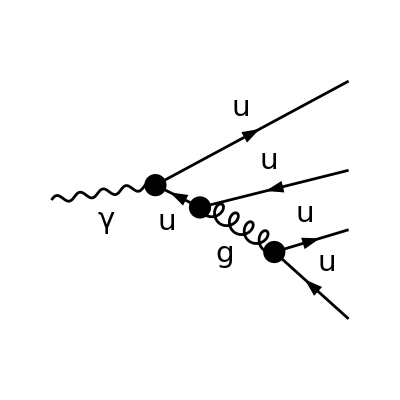

```mathematica
$top = CreateTopologies[0, 1 -> 4];
$dall = InsertFields[$top,{V[1]}->{F[3, {1}], -F[3, {1}],F[3, {1}], -F[3, {1}]},
		InsertionLevel -> {Classes}, Model -> "SMQCD", ExcludeParticles -> {S[1], S[2],V[1], V[2]}];
$dtag="_2";
$diag=$D[{2}];
Paint[$diag, ColumnsXRows -> {2, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
$amp=FCFAConvert[CreateFeynAmp[$diag,Truncated -> False],IncomingMomenta->{q},
OutgoingMomenta->{p1,p2,p3,p4},UndoChiralSplittings->True,DropSumOver->True,List->False,SMP->True]//Contract//ChangeDimension[#,n]&
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

2/3 Spinor[Momentum[p3,n],SMP[m_u],1].DiracGamma[LorentzIndex[Lor2,n],n].Spinor[-Momentum[p4,n],SMP[m_u],1] Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[q,ⅈ],n],n].(DiracGamma[Momentum[-p2-p3-p4,n],n]+SMP[m_u]).DiracGamma[LorentzIndex[Lor2,n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[Momentum[p3,n]+Momentum[p4,n],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[p2,n]+Momentum[p3,n]+Momentum[p4,n],SMP[m_u]]] SMP[e] SMP[g_s]^2 SUNTF[{SUNIndex[Glu6]},SUNFIndex[Col2],SUNFIndex[Col3]] SUNTF[{SUNIndex[Glu6]},SUNFIndex[Col4],SUNFIndex[Col5]]

```mathematica
SetMandelstam[s,{-q,p1,p2,p3,p4},{1,0,0,0,0}];
```

```mathematica
$me2=$amp*(ComplexConjugate[$amp]//FCRenameDummyIndices)//
PropagatorDenominatorExplicit//FermionSpinSum//ReplaceAll[#,{DiracTrace->Tr}]&//DoPolarizationSums[#,q,0,VirtualBoson->True,GaugeTrickN->4]&(*//DoPolarizationSums[#,p3,0]&//DoPolarizationSums[#,p4,0]&*);
```

```mathematica
$r1=$me2//SUNSimplify[#,SUNNToCACF->False]&;
```

```mathematica
$r2=$r1/.{SUNN->3,SMP["m_u"]->0,SMP["g_s"]->1,SMP["e"]->1}
```

(256 (1/2-1/2 s[1,2]-1/2 s[1,5]+1/2 s[3,4]) s[3,4])/(9 s[1,2] s[4,5]^2)-(128 n (1/2-1/2 s[1,2]-1/2 s[1,5]+1/2 s[3,4]) s[3,4])/(9 s[1,2] s[4,5]^2)+(512 (1/2 s[1,5]-1/2 s[2,3]-1/2 s[3,4]) (1/2 s[1,2]-1/2 s[3,4]-1/2 s[4,5]))/(9 s[1,2] s[4,5]^2)-(256 n (1/2 s[1,5]-1/2 s[2,3]-1/2 s[3,4]) (1/2 s[1,2]-1/2 s[3,4]-1/2 s[4,5]))/(9 s[1,2] s[4,5]^2)-(512 n (-1/2+1/2 s[1,2]) s[3,4] (1/2 s[1,2]-1/2 s[3,4]-1/2 s[4,5]))/(9 s[1,2]^2 s[4,5]^2)-(512 s[2,3] s[3,4] (1/2 s[1,2]-1/2 s[3,4]-1/2 s[4,5]))/(9 s[1,2]^2 s[4,5]^2)-(1024 (1/2 s[1,5]-1/2 s[2,3]-1/2 s[3,4]) s[3,4] (1/2 s[1,2]-1/2 s[3,4]-1/2 s[4,5]))/(9 s[1,2]^2 s[4,5]^2)-(1024 (1/2-1/2 s[1,2]-1/2 s[1,5]+1/2 s[3,4]) s[3,4] (1/2 s[1,2]-1/2 s[3,4]-1/2 s[4,5]))/(9 s[1,2]^2 s[4,5]^2)-(256 s[2,3])/(9 s[1,2] s[4,5])+(64 n s[2,3])/(3 s[1,2] s[4,5])-(32 n^2 s[2,3])/(9 s[1,2] s[4,5])+(128 n (-1/2+1/2 s[1,2]) (s[1,2]-s[4,5]))/(9 s[1,2]^2 s[4,5])-(64 n^2 (-1/2+1/2 s[1,2]) (s[1,2]-s[4,5]))/(9 s[1,2]^2 s[4,5])+(128 s[2,3] (s[1,2]-s[4,5]))/(9 s[1,2]^2 s[4,5])-(64 n s[2,3] (s[1,2]-s[4,5]))/(9 s[1,2]^2 s[4,5])+(256 (1/2 s[1,5]-1/2 s[2,3]-1/2 s[3,4]) (s[1,2]-s[4,5]))/(9 s[1,2]^2 s[4,5])-(128 n (1/2 s[1,5]-1/2 s[2,3]-1/2 s[3,4]) (s[1,2]-s[4,5]))/(9 s[1,2]^2 s[4,5])+(256 (1/2-1/2 s[1,2]-1/2 s[1,5]+1/2 s[3,4]) (s[1,2]-s[4,5]))/(9 s[1,2]^2 s[4,5])-(128 n (1/2-1/2 s[1,2]-1/2 s[1,5]+1/2 s[3,4]) (s[1,2]-s[4,5]))/(9 s[1,2]^2 s[4,5])

```mathematica
$res = $r2/.Rule[Explicit,False]->Rule[Explicit,True]//Expand//SUNSimplify[#,SUNNToCACF->False]&
```

-128/(9 s[1,2]^2)+(128 n)/(9 s[1,2]^2)-(32 n^2)/(9 s[1,2]^2)+128/(9 s[1,2])-(128 n)/(9 s[1,2])+(32 n^2)/(9 s[1,2])+(128 s[1,5])/(9 s[4,5]^2)-(64 n s[1,5])/(9 s[4,5]^2)-(128 s[2,3])/(9 s[4,5]^2)+(64 n s[2,3])/(9 s[4,5]^2)-(128 s[3,4])/(9 s[1,2] s[4,5]^2)+(64 n s[3,4])/(9 s[1,2] s[4,5]^2)-(256 s[1,5] s[3,4])/(9 s[1,2] s[4,5]^2)+(128 n s[1,5] s[3,4])/(9 s[1,2] s[4,5]^2)+(128 s[2,3] s[3,4])/(9 s[1,2] s[4,5]^2)-(64 n s[2,3] s[3,4])/(9 s[1,2] s[4,5]^2)+(256 s[3,4]^2)/(9 s[1,2]^2 s[4,5]^2)-(128 n s[3,4]^2)/(9 s[1,2]^2 s[4,5]^2)-128/(9 s[4,5])+(128 n)/(9 s[4,5])-(32 n^2)/(9 s[4,5])+128/(9 s[1,2] s[4,5])-(128 n)/(9 s[1,2] s[4,5])+(32 n^2)/(9 s[1,2] s[4,5])-(128 s[1,5])/(9 s[1,2] s[4,5])+(64 n s[1,5])/(9 s[1,2] s[4,5])-(128 s[2,3])/(9 s[1,2] s[4,5])+(128 n s[2,3])/(9 s[1,2] s[4,5])-(32 n^2 s[2,3])/(9 s[1,2] s[4,5])+(256 s[3,4])/(9 s[1,2]^2 s[4,5])-(128 n s[3,4])/(9 s[1,2]^2 s[4,5])-(128 s[3,4])/(9 s[1,2] s[4,5])+(64 n s[3,4])/(9 s[1,2] s[4,5])

```mathematica
Put[9/4 $res/.{n->4-2ep,SUNN->3},"~/src/eec@nlo/real/me2/test/a2qqqq_0_0"<>$dtag<>".m"]
```

```mathematica
$res/.n->4//Simplify
```

-(128 (2 s[3,4]^2+2 s[3,4] s[4,5]+s[4,5]^2+s[1,2]^2 (s[1,5]-s[2,3]+s[4,5])-s[1,2] (s[4,5] (1+s[1,5]-s[2,3]+s[4,5])+s[3,4] (1+2 s[1,5]-s[2,3]+s[4,5]))))/(9 s[1,2]^2 s[4,5]^2)